```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=4;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

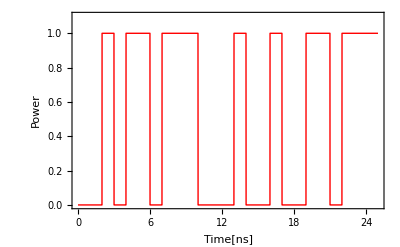

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*10^-9<t<(i+1)*10^-9,1,0],If[i*10^-9<t<(i+1)*10^-9,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-9],{t,0,bit},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ns]","Power"},BaseStyle->{Bold,FontSize->20},PlotRange->{0,1.1}]
```

1/2 (1+Cos[400000000000000 π t])

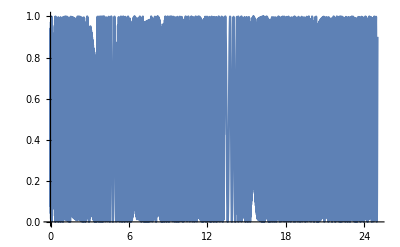

1/2 (1+Cos[400000000000000 π t]) (If[1/1000000000<t<1/500000000,0,0]+If[1/500000000<t<3/1000000000,1,0]+If[3/1000000000<t<1/250000000,0,0]+If[1/250000000<t<1/200000000,1,0]+If[1/200000000<t<3/500000000,1,0]+If[3/500000000<t<7/1000000000,0,0]+If[7/1000000000<t<1/125000000,1,0]+If[1/125000000<t<9/1000000000,1,0]+If[9/1000000000<t<1/100000000,1,0]+If[1/100000000<t<11/1000000000,0,0]+If[11/1000000000<t<3/250000000,0,0]+If[3/250000000<t<13/1000000000,0,0]+If[13/1000000000<t<7/500000000,1,0]+If[7/500000000<t<3/200000000,0,0]+If[3/200000000<t<1/62500000,0,0]+If[1/62500000<t<17/1000000000,1,0]+If[17/1000000000<t<9/500000000,0,0]+If[9/500000000<t<19/1000000000,0,0]+If[19/1000000000<t<1/50000000,1,0]+If[1/50000000<t<21/1000000000,1,0]+If[21/1000000000<t<11/500000000,0,0]+If[11/500000000<t<23/1000000000,1,0]+If[23/1000000000<t<3/125000000,1,0]+If[3/125000000<t<1/40000000,1,0]+If[1/40000000<t<13/500000000,1,0])

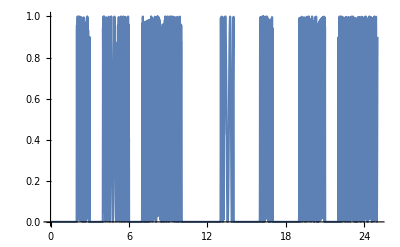

```mathematica
Fc= 200 *10^12;(*搬送波の周波数[THz]*)
carrier[t_]= (1+Cos[2*Pi*Fc*t])/2
Plot[carrier[t*10^-9], {t,0,25}]
cs[t_]=signal[t]*carrier[t]
Plot[cs[t*10^-9],{t,0,25}]
```

```mathematica
∫_0^(bit*10^-9) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-((ⅈ ⅇ^(-(ⅈ f π)/20000000) (-1+ⅇ^((ⅈ f π)/500000000)) (1+ⅇ^((ⅈ f π)/500000000)+ⅇ^((ⅈ f π)/250000000)+ⅇ^((ⅈ f π)/125000000)+ⅇ^((ⅈ f π)/100000000)+ⅇ^((ⅈ f π)/62500000)+ⅇ^((11 ⅈ f π)/500000000)+ⅇ^((3 ⅈ f π)/100000000)+ⅇ^((ⅈ f π)/31250000)+ⅇ^((17 ⅈ f π)/500000000)+ⅇ^((19 ⅈ f π)/500000000)+ⅇ^((ⅈ f π)/25000000)+ⅇ^((11 ⅈ f π)/250000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π))

```mathematica
fc[f_]:=-(ⅈ ⅇ^(-(7 ⅈ f π)/250000000) (-1+ⅇ^((ⅈ f π)/500000000)) (1+ⅇ^((ⅈ f π)/125000000)+ⅇ^((ⅈ f π)/100000000)+ⅇ^((3 ⅈ f π)/250000000)+ⅇ^((ⅈ f π)/62500000)+ⅇ^((9 ⅈ f π)/500000000)+ⅇ^((11 ⅈ f π)/500000000)) (-20000000000000000000000000000+f^2))/(2 f (-40000000000000000000000000000+f^2) π)
```

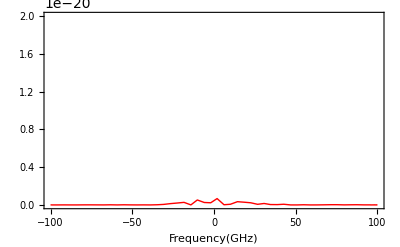

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-1*^2,1*^2},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(GHz)"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

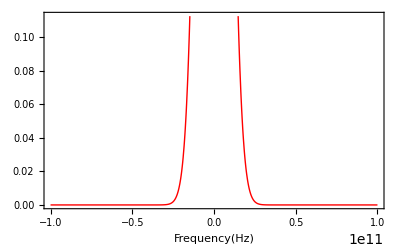

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-9],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

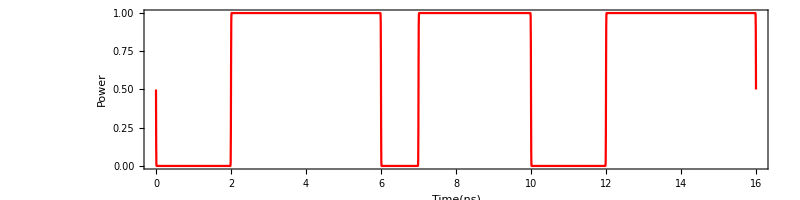

```mathematica
Plot[nrzsig[t*10^-9],{t,0,bit},Frame->True,FrameLabel->{"Time(ns)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
(*f[x_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]*)
```

```mathematica
(*max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]*)
```

## Impulse Responce for Fiber Dispersion

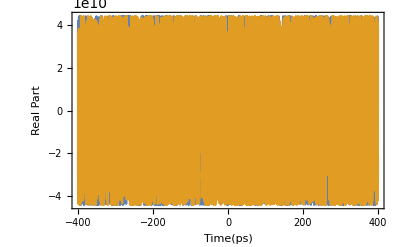

```mathematica
hdis[t_]:=1/(√(2*Pi*β2*L))*Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-9],Im@hdis[t*10^-9]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
(*hcmp[t_]:=1/2(1/(√(2*Pi*β2*60))*10^6*Exp[+ⅈ*(t^2/(2*β2*60)-Pi/4)]+

1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(t^2/(2*β2*80)-Pi/4)]);*)
```

```mathematica
(*Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]*)
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
(*For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]*)
```

```mathematica
(*IntegerPart[total*10^12]*)
```

```mathematica
For[i=-100.,i≤bit+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-9];If[Mod[i,500]==0,Print[i]]]
```

0.

```mathematica
(*For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]*)
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-9]]
```

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

-Graphics-

## Simulation

```mathematica
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*hdis2[a-t],{t,-100,bit+100,samp}]
```

```mathematica
simu1[-100.]
```

5.45788×10^11+1.18338×10^11 ⅈ

```mathematica
For[i=-100.,i≤bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,bit+100,samp}]
```

{{-100.,5.5847×10^11},{-99.5,4.70968×10^11},{-99.,7.90032×10^11},{-98.5,1.09221×10^12},{-98.,9.58789×10^11},{-97.5,8.45295×10^11},{-97.,8.05503×10^11},{-96.5,6.89159×10^11},{-96.,5.92413×10^11},{-95.5,5.79894×10^11},{-95.,7.28083×10^11},{-94.5,7.78406×10^11},{-94.,8.54161×10^11},{-93.5,1.0256×10^12},{-93.,1.1156×10^12},{-92.5,1.08234×10^12},{-92.,9.12452×10^11},{-91.5,5.10834×10^11},{-91.,2.62072×10^11},{-90.5,3.6127×10^11},{-90.,6.10709×10^11},{-89.5,6.68515×10^11},{-89.,9.14428×10^11},{-88.5,1.26293×10^12},{-88.,1.16518×10^12},{-87.5,1.00466×10^12},{-87.,8.70067×10^11},{-86.5,7.29484×10^11},{-86.,6.65557×10^11},{-85.5,6.68674×10^11},{-85.,9.45862×10^11},{-84.5,9.87155×10^11},{-84.,1.06199×10^12},{-83.5,1.25973×10^12},{-83.,1.38722×10^12},{-82.5,1.43874×10^12},{-82.,1.2461×10^12},{-81.5,8.55518×10^11},{-81.,6.41832×10^11},{-80.5,6.94998×10^11},{-80.,1.0279×10^12},{-79.5,1.06627×10^12},{-79.,1.18408×10^12},{-78.5,1.35091×10^12},{-78.,1.20758×10^12},{-77.5,1.05641×10^12},{-77.,9.84463×10^11},{-76.5,8.43265×10^11},{-76.,7.43689×10^11},{-75.5,7.88763×10^11},{-75.,1.03768×10^12},{-74.5,1.01581×10^12},{-74.,9.60062×10^11},{-73.5,1.23237×10^12},{-73.,1.28806×10^12},{-72.5,1.24519×10^12},{-72.,1.0255×10^12},{-71.5,7.69016×10^11},{-71.,5.91482×10^11},{-70.5,6.94151×10^11},{-70.,1.08766×10^12},{-69.5,1.05545×10^12},{-69.,8.88542×10^11},{-68.5,1.01863×10^12},{-68.,9.3593×10^11},{-67.5,9.06038×10^11},{-67.,8.78545×10^11},{-66.5,7.44556×10^11},{-66.,6.12708×10^11},{-65.5,8.05381×10^11},{-65.,1.12811×10^12},{-64.5,1.0584×10^12},{-64.,1.03212×10^12},{-63.5,1.29738×10^12},{-63.,1.40767×10^12},{-62.5,1.32431×10^12},{-62.,1.17017×10^12},{-61.5,9.22958×10^11},{-61.,7.1705×10^11},{-60.5,7.01852×10^11},{-60.,1.1141×10^12},{-59.5,1.16338×10^12},{-59.,1.10395×10^12},{-58.5,1.28274×10^12},{-58.,1.25619×10^12},{-57.5,1.22565×10^12},{-57.,1.16731×10^12},{-56.5,8.59634×10^11},{-56.,7.1726×10^11},{-55.5,8.72634×10^11},{-55.,1.17725×10^12},{-54.5,1.03442×10^12},{-54.,9.68394×10^11},{-53.5,1.2325×10^12},{-53.,1.30041×10^12},{-52.5,1.21518×10^12},{-52.,1.05642×10^12},{-51.5,9.0439×10^11},{-51.,6.8052×10^11},{-50.5,5.80533×10^11},{-50.,8.65564×10^11},{-49.5,8.97601×10^11},{-49.,9.10007×10^11},{-48.5,1.07271×10^12},{-48.,9.85291×10^11},{-47.5,1.02191×10^12},{-47.,1.02662×10^12},{-46.5,7.94804×10^11},{-46.,7.61577×10^11},{-45.5,8.66034×10^11},{-45.,1.09113×10^12},{-44.5,1.00318×10^12},{-44.,9.24371×10^11},{-43.5,1.02982×10^12},{-43.,1.05667×10^12},{-42.5,9.56904×10^11},{-42.,7.89554×10^11},{-41.5,6.41981×10^11},{-41.,5.11398×10^11},{-40.5,5.53476×10^11},{-40.,7.61413×10^11},{-39.5,6.95998×10^11},{-39.,7.3615×10^11},{-38.5,8.82949×10^11},{-38.,8.75404×10^11},{-37.5,8.70685×10^11},{-37.,8.43563×10^11},{-36.5,7.01554×10^11},{-36.,6.76745×10^11},{-35.5,8.16015×10^11},{-35.,1.11189×10^12},{-34.5,1.00653×10^12},{-34.,8.4912×10^11},{-33.5,9.49198×10^11},{-33.,9.44889×10^11},{-32.5,7.24315×10^11},{-32.,5.3123×10^11},{-31.5,3.84554×10^11},{-31.,3.74938×10^11},{-30.5,5.13953×10^11},{-30.,7.10778×10^11},{-29.5,7.14993×10^11},{-29.,8.11886×10^11},{-28.5,9.17142×10^11},{-28.,7.94713×10^11},{-27.5,6.93675×10^11},{-27.,7.19891×10^11},{-26.5,6.80766×10^11},{-26.,7.0114×10^11},{-25.5,9.66124×10^11},{-25.,1.21573×10^12},{-24.5,1.14835×10^12},{-24.,9.51606×10^11},{-23.5,1.02477×10^12},{-23.,9.72793×10^11},{-22.5,7.7262×10^11},{-22.,5.88873×10^11},{-21.5,4.69487×10^11},{-21.,6.03853×10^11},{-20.5,8.07181×10^11},{-20.,9.34538×10^11},{-19.5,9.4654×10^11},{-19.,8.95401×10^11},{-18.5,9.65663×10^11},{-18.,8.65124×10^11},{-17.5,8.75573×10^11},{-17.,7.96557×10^11},{-16.5,7.20733×10^11},{-16.,7.11574×10^11},{-15.5,8.66642×10^11},{-15.,1.16788×10^12},{-14.5,1.0376×10^12},{-14.,9.25023×10^11},{-13.5,9.39348×10^11},{-13.,9.00334×10^11},{-12.5,7.32691×10^11},{-12.,6.32991×10^11},{-11.5,5.01199×10^11},{-11.,5.63103×10^11},{-10.5,7.57255×10^11},{-10.,9.14379×10^11},{-9.5,8.18077×10^11},{-9.,7.13373×10^11},{-8.5,8.12331×10^11},{-8.,8.12036×10^11},{-7.5,8.30844×10^11},{-7.,7.48272×10^11},{-6.5,6.75665×10^11},{-6.,6.85361×10^11},{-5.5,8.90858×10^11},{-5.,1.25266×10^12},{-4.5,1.17753×10^12},{-4.,1.06181×10^12},{-3.5,1.08439×10^12},{-3.,9.38251×10^11},{-2.5,8.19497×10^11},{-2.,7.27316×10^11},{-1.5,5.68109×10^11},{-1.,6.2401×10^11},{-0.5,6.5207×10^11},{0.,8.87919×10^11},{0.5,8.7766×10^11},{1.,8.83652×10^11},{1.5,9.88323×10^11},{2.,9.19404×10^11},{2.5,8.25584×10^11},{3.,6.82727×10^11},{3.5,6.46626×10^11},{4.,6.48163×10^11},{4.5,8.17792×10^11},{5.,1.22787×10^12},{5.5,1.24678×10^12},{6.,1.18303×10^12},{6.5,1.15472×10^12},{7.,9.9743×10^11},{7.5,8.55911×10^11},{8.,7.18269×10^11},{8.5,6.25766×10^11},{9.,7.41376×10^11},{9.5,6.73686×10^11},{10.,7.11573×10^11},{10.5,7.92947×10^11},{11.,8.1756×10^11},{11.5,9.8677×10^11},{12.,1.01877×10^12},{12.5,9.54501×10^11},{13.,7.5704×10^11},{13.5,5.57991×10^11},{14.,5.54027×10^11},{14.5,7.84791×10^11},{15.,1.22481×10^12},{15.5,1.19412×10^12},{16.,1.1214×10^12},{16.5,1.15945×10^12},{17.,1.07557×10^12},{17.5,9.10052×10^11},{18.,8.31805×10^11},{18.5,6.92526×10^11},{19.,7.33095×10^11},{19.5,6.90748×10^11},{20.,8.02012×10^11},{20.5,7.84032×10^11},{21.,6.32132×10^11},{21.5,7.79695×10^11},{22.,9.22344×10^11},{22.5,9.66134×10^11},{23.,8.56439×10^11},{23.5,6.45236×10^11},{24.,5.19541×10^11},{24.5,6.78799×10^11},{25.,1.09857×10^12},{25.5,1.05146×10^12},{26.,9.28681×10^11},{26.5,9.93762×10^11},{27.,9.57359×10^11},{27.5,9.08953×10^11},{28.,8.6183×10^11},{28.5,7.12351×10^11},{29.,6.90244×10^11},{29.5,6.70421×10^11},{30.,7.84169×10^11},{30.5,7.86146×10^11},{31.,7.02077×10^11},{31.5,8.25496×10^11},{32.,9.35999×10^11},{32.5,8.50327×10^11},{33.,7.12156×10^11},{33.5,5.87523×10^11},{34.,4.22464×10^11},{34.5,6.87969×10^11},{35.,1.04202×10^12},{35.5,1.08424×10^12},{36.,1.01462×10^12},{36.5,1.12127×10^12},{37.,1.1025×10^12},{37.5,1.04141×10^12},{38.,9.91055×10^11},{38.5,7.39566×10^11},{39.,6.98197×10^11},{39.5,7.08545×10^11},{40.,7.53891×10^11},{40.5,7.886×10^11},{41.,7.23988×10^11},{41.5,8.27235×10^11},{42.,8.30969×10^11},{42.5,7.53012×10^11},{43.,6.87448×10^11},{43.5,6.10041×10^11},{44.,5.26378×10^11},{44.5,7.48888×10^11},{45.,1.07572×10^12},{45.5,1.0619×10^12},{46.,1.02316×10^12},{46.5,1.07307×10^12},{47.,9.43163×10^11},{47.5,7.82239×10^11},{48.,7.26161×10^11},{48.5,4.6916×10^11},{49.,5.53355×10^11},{49.5,6.43921×10^11},{50.,7.43106×10^11},{50.5,7.19849×10^11},{51.,5.77902×10^11},{51.5,6.91845×10^11},{52.,7.42651×10^11},{52.5,7.28909×10^11},{53.,7.07645×10^11},{53.5,6.14625×10^11},{54.,6.22491×10^11},{54.5,8.17177×10^11},{55.,1.06628×10^12},{55.5,1.0476×10^12},{56.,9.80054×10^11},{56.5,1.00919×10^12},{57.,9.25862×10^11},{57.5,8.22281×10^11},{58.,8.77296×10^11},{58.5,6.30255×10^11},{59.,6.46969×10^11},{59.5,8.44159×10^11},{60.,8.43319×10^11},{60.5,8.14243×10^11},{61.,6.90635×10^11},{61.5,7.72916×10^11},{62.,8.27986×10^11},{62.5,8.0389×10^11},{63.,8.66381×10^11},{63.5,7.5814×10^11},{64.,8.15191×10^11},{64.5,1.08238×10^12},{65.,1.23187×10^12},{65.5,1.20422×10^12},{66.,1.06286×10^12},{66.5,1.05218×10^12},{67.,9.43797×10^11},{67.5,8.23988×10^11},{68.,9.28879×10^11},{68.5,6.69892×10^11},{69.,7.54757×10^11},{69.5,1.0081×10^12},{70.,1.20322×10^12},{70.5,1.16764×10^12},{71.,8.17486×10^11},{71.5,8.60046×10^11},{72.,9.1133×10^11},{72.5,9.34909×10^11},{73.,1.03113×10^12},{73.5,8.67536×10^11},{74.,9.80804×10^11},{74.5,1.36959×10^12},{75.,1.50632×10^12},{75.5,1.43621×10^12},{76.,1.2904×10^12},{76.5,1.29055×10^12},{77.,1.07977×10^12},{77.5,9.69157×10^11},{78.,9.85149×10^11},{78.5,6.52934×10^11},{79.,6.66982×10^11},{79.5,1.0325×10^12},{80.,1.2379×10^12},{80.5,1.17971×10^12},{81.,9.39588×10^11},{81.5,9.58245×10^11},{82.,9.67485×10^11},{82.5,9.49358×10^11},{83.,1.04331×10^12},{83.5,8.20763×10^11},{84.,7.78494×10^11},{84.5,1.15358×10^12},{85.,1.24438×10^12},{85.5,1.11078×10^12},{86.,1.04296×10^12},{86.5,1.08342×10^12},{87.,9.7284×10^11},{87.5,8.35591×10^11},{88.,8.57271×10^11},{88.5,5.80905×10^11},{89.,5.39184×10^11},{89.5,9.40244×10^11},{90.,1.16554×10^12},{90.5,1.18673×10^12},{91.,9.90637×10^11},{91.5,9.76027×10^11},{92.,8.83842×10^11},{92.5,8.1896×10^11},{93.,1.00541×10^12},{93.5,8.38512×10^11},{94.,8.39188×10^11},{94.5,1.18272×10^12},{95.,1.36132×10^12},{95.5,1.33192×10^12},{96.,1.25472×10^12},{96.5,1.3026×10^12},{97.,1.19179×10^12},{97.5,9.95817×10^11},{98.,8.37744×10^11},{98.5,6.08005×10^11},{99.,8.39059×10^11},{99.5,1.22889×10^12},{100.,1.3135×10^12},{100.5,1.26452×10^12},{101.,1.02817×10^12},{101.5,9.61808×10^11},{102.,7.76651×10^11},{102.5,6.69384×10^11},{103.,9.19369×10^11},{103.5,8.01334×10^11},{104.,7.95163×10^11},{104.5,1.09428×10^12},{105.,1.32418×10^12},{105.5,1.26012×10^12},{106.,1.07264×10^12},{106.5,9.65565×10^11},{107.,7.96852×10^11},{107.5,4.65385×10^11},{108.,3.83044×10^11},{108.5,2.70863×10^11},{109.,5.76038×10^11},{109.5,9.37684×10^11},{110.,1.03203×10^12},{110.5,9.60295×10^11},{111.,8.33109×10^11},{111.5,7.43223×10^11},{112.,6.05988×10^11},{112.5,4.96988×10^11},{113.,8.11248×10^11},{113.5,7.83991×10^11},{114.,7.13545×10^11},{114.5,9.96989×10^11},{115.,1.22927×10^12},{115.5,1.1109×10^12},{116.,9.0305×10^11}}

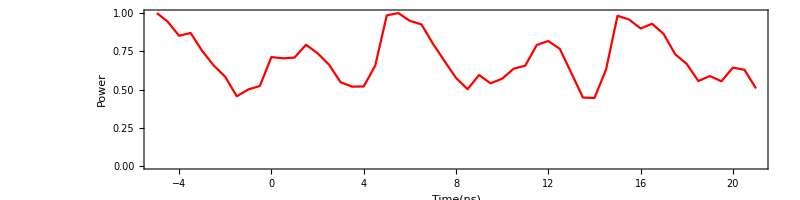

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,bit+5,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-5,bit+5,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ns)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 8

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

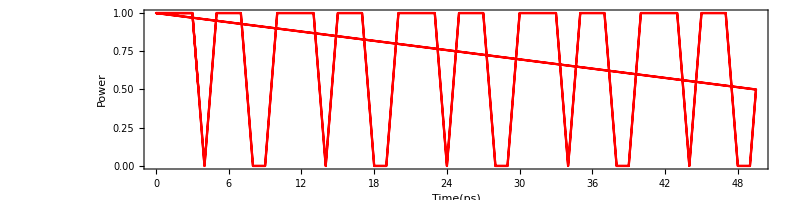

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

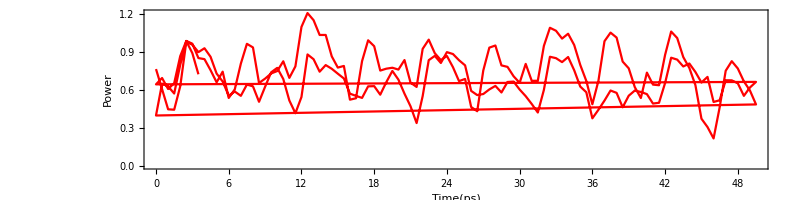

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 20 point

0 is 2 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.784033

Average of 0 is 0.449193

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.125583

A Standard Deviation of 0 is 0.0167316

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

General::munfl: Exp[-1235.65]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: Exp[-1.2872×10^6]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

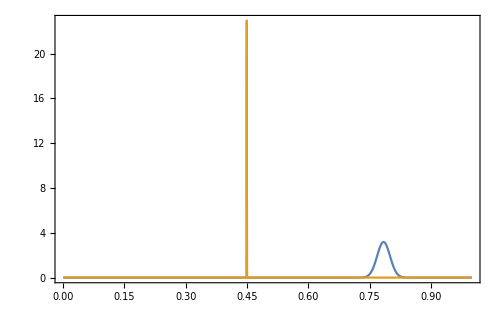

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 2.35282

Q-dB is 7.43177 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 0.00931583

Eye Opening is 0.574978

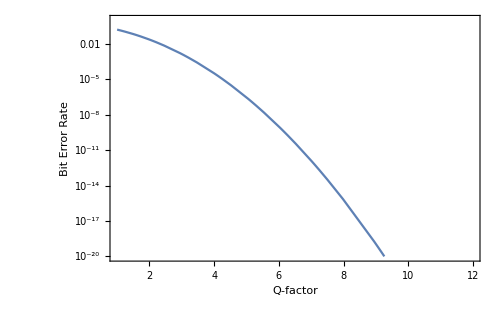

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```